```mathematica
m=10;
```

```mathematica
b=6;
```

```mathematica
c=60;
```

```mathematica
a1=1;
```

```mathematica
V=6.15;
```

```mathematica
a3=1;
```

```mathematica
s=NDSolve[{m*y''[t]+b*y'[t]+c*y[t]==V*a1*y'[t]-a3*(y'[t])^3/V,y[0]==0.5,y'[0]==10},y,{t,0,400}]
```

{{y→InterpolatingFunction[{{0.,400.}},<>]}}

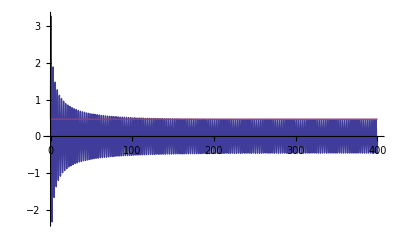

```mathematica
Plot[{Evaluate[y[t] /. s],(2/Sqrt[3])*Sqrt[m/c]}, {t,0, 400}, PlotRange->All]
```

```mathematica
ParametricPlot[Evaluate[{y[t],y'[t]} /. s],{t,0,100}]
```

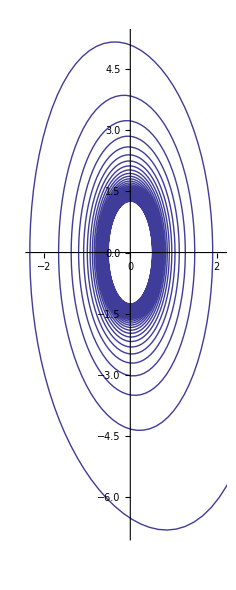
```mathematica
-Graphics-w
```

```mathematica
V*a1
```

5.001

```mathematica
V*a1-b
```

0.001

```mathematica
b
```

5

```mathematica
FullSimplify[Exp[Integrate[1/(A/2+3A^3ω^2/8),A]]]
```

A^2/(4+3 A^2)

```mathematica
ω=1;
```

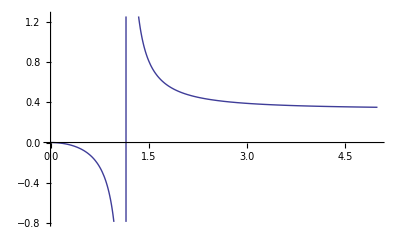

```mathematica
Plot[A^2/(3*A^2*ω^2-4),{A,0,5}]
```